```mathematica
Didascalia[Color_,Property_]:=
Show[
	ListPlot[
			{{0,0}},
			Axes->None,
			PlotMarkers ->{Automatic,10},
			PlotStyle-> Directive[Color],
			AspectRatio ->.1
			],
	ListLinePlot[
				{{-1,0},{1,0}},
				Axes->None,
				PlotStyle->Directive[Thick,Color,Property]
				]
	];
```

```mathematica
CaptionGeneral[content_]:=Framed[Grid
[
Table[{Didascalia[content[[i]][[2]],content[[i]][[3]]],content[[i]][[1]]},{i,1,Dimensions[content][[1]]}]
]
]
```

```mathematica
Contenuto={{"Testo",Black,Dashed},{"AltroTesto",Blue,Dotted},{"Third text",Orange,Thin},{"Prova",Purple,Dashing[{0.05,0.05}]}}
```

{{Testo,-Graphics-,Dashing[{Small,Small}]},{AltroTesto,-Graphics-,Dashing[{0,Small}]},{Third text,-Graphics-,Thickness[Tiny]},{Prova,-Graphics-,Dashing[{0.05,0.05}]}}

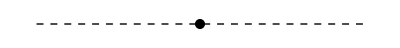
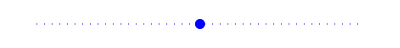
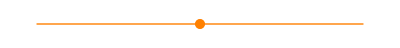
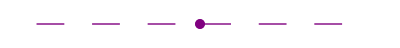
-Graphics- | Testo
-Graphics- | AltroTesto
-Graphics- | Third text
-Graphics- | Prova

```mathematica
CaptionGeneral[Contenuto]
```

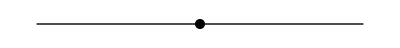
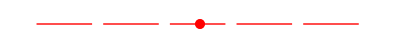
-Graphics- | GONG data
-Graphics- | Radiative solution

```mathematica
Contenuto={{"GONG data",Black,Automatic},{"Radiative solution",Red,Dashing[{0.1,0.02}]}};
LegendKey=CaptionGeneral[Contenuto]
```

```mathematica
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\NAM2015 - Presentation\\Code\\LegendKey.png",LegendKey,ImageResolution->150]
```

C:\Users\Pigkappa\Dropbox\fisica\PhD\NAM2015 - Presentation\Code\LegendKey.png

```mathematica
LegendKey2={{-Graphics-, "GONG data"}, {-Graphics-, "v=0 solution"}}
```

-Graphics- | GONG data
-Graphics- | v=0 solution

```mathematica
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\NAM2015 - Presentation\\Code\\LegendKey2.png",LegendKey2,ImageResolution->150]
```

C:\Users\Pigkappa\Dropbox\fisica\PhD\NAM2015 - Presentation\Code\LegendKey2.png